```mathematica
<<Local`QFTToolKit`
DefineTensorShortcuts[{{Q},1},{{σ},4}]
QCDBaseIndices
DefineDottedIndices
```

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3,4,5,6,7,8}},{color,{1,2,3}},{flavor,{1,2,3,4,5,6}},{family,{1,2,3}}}

```mathematica
DefineTensorShortcuts[{{η,t,δ,ε},1},
{{σ},3}
]
```

Lecture 4 (9 Sept 2011)

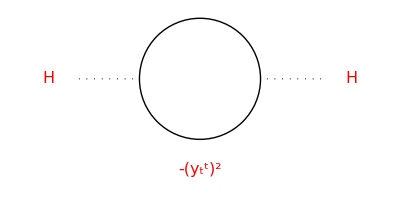
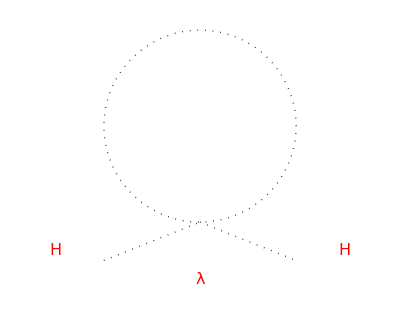
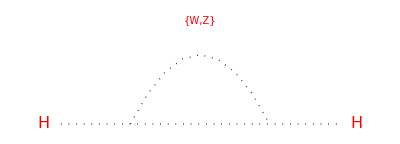
Some problems with the Standard Model lagrangian in that it predicts quadratic divergences from higher order Higgs mass terms which require fine tuning to cancel:ℒ→μ^2 H^†.H+λ (H^†.H)^2 with diagrams -Graphics- and -Graphics- and -Graphics-
Possible solutions: ()cancelation of quadradic terms, ()Higgs not fundamental [other diagrams], ()no Higgs.

```mathematica
scale=1;
MidArrow[xy_]:={Arrow[{xy[[1]],(xy[[1]]+xy[[2]])/2}],Line[{(xy[[1]]+xy[[2]])/2,xy[[2]]}]};
TextOver[text_,xy_]:={White,Disk[xy,0.2scale],
Text[Style[text,FontSize->16,Red],xy]};
Graphics121[x_]:=Graphics[{Thick,Black,
Circle[{0,0},scale],
Dotted,Line[{{-2 scale,0},{-1 scale,0}}],
Line[{{2 scale,0},{1 scale,0}}],
TextOver[x,{0,-1.3 scale}]
}
];
Graphics121[x_,x0_,x1_]:=Graphics[{Thick,Black,
Circle[{0,0},scale],
Dotted,Line[{{-2 scale,0},{-1 scale,0}}],
Line[{{2 scale,0},{1 scale,0}}],
TextOver[x,{0,-1.5scale}],
TextOver[x0,{-2.5,0}],TextOver[x1,{2.5,0}]
}
];
Graphics20[x_]:=Graphics[{Thick,Black,Dotted,
Circle[{0,0},scale],
Line[{{-scale,-1.2 scale},{ 0,-scale}}],
Line[{{0,-scale},{ scale,-1.6 scale}}],
TextOver[x,{0,-1.3 scale}]
}
];
Graphics20[x_,x0_,x1_]:=Graphics[{Thick,Black,Dotted,
Circle[{0,0},scale],
Line[{{-scale,-1.4 scale},{ 0,-scale}}],
Line[{{0,-scale},{ scale,-1.4scale}}],
TextOver[x,{0,-1.6 scale}],
TextOver[x0,{-1.5,-1.3}],TextOver[x1,{1.5,-1.3}]
}
];
Graphics12d1[x_,x0_,x1_]:=Graphics[{Thick,Black,Dotted,
Line[{{-4 ,0},{4 ,0}}],
BezierCurve[{{-2,0},{0,4},{2,0}}],
TextOver[x,{0,3. },10],
TextOver[x0,{-4.5,0}],TextOver[x1,{4.5,-0}]
}
];
PR1["Some problems with the Standard Model lagrangian in that it predicts quadratic divergences from higher order Higgs mass terms which require fine tuning to cancel:",
ℒ->μ μ SuperDagger[H].H+λ (SuperDagger[H].H)^2," with diagrams ",
Graphics121[-yd[t]^2,H,H],and,
Graphics20[λ,H,H],and,
Graphics12d1[{W,Z},H,H],
NL,"Possible solutions: ()cancelation of quadradic terms, ()Higgs not fundamental [other diagrams], ()no Higgs. "
];
```

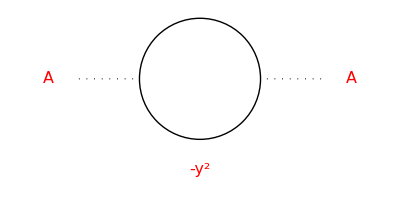
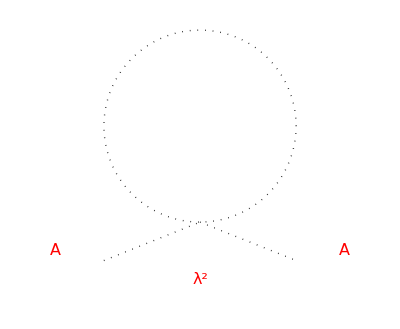
The following is a Toy model to show quadratic divergence features which allude to SUSY.  Assume fields {A,ψ_α^α} where A is a scalar field and ψ_α^α is a fermionic field.
We take the interaction Lagrangian (with coupling parameters {y,λ}) to be
→ ℒ_int→-A y ψ.ψ-λ^2 (A^†.A)^2
and the mass Lagrangian to be
→ ℒ_mass→A^†.A m_A^2-m_ψ (ψ.ψ+(ψ.ψ)^†)
The A self-energy diagram from :-A y ψ.ψ ⟶ -Graphics-
The A self-energy diagram from :-λ^2 (A^†.A)^2 ⟶ -Graphics-
These self-energy terms cancel if λ==y and λ≫{m_ψ,m_A}

```mathematica
PR1["The following is a Toy model to show quadratic divergence features which allude to SUSY.  Assume fields ",
tmp={A,ψd[α]}," where ",tmp[[1]]," is a scalar field and ",tmp[[2]]," is a fermionic field.",
NL,"We take the interaction Lagrangian (with coupling parameters {y,λ}) to be",Yield,
tmpLi=Subscript[ℒ, int]->-y A (ψ.ψ)-λ^2(SuperDagger[A].A)^2,
NL,"and the mass Lagrangian to be",Yield,
tmpLm=Subscript[ℒ, mass]->Subscript[m, A]^2 SuperDagger[A].A-Subscript[m, ψ](ψ.ψ+SuperDagger[(ψ.ψ)]),
NL,"The A self-energy diagram from :",tmpLi[[2,1]],yield,
Graphics121[-y^2,A,A],
NL,"The A self-energy diagram from :",tmpLi[[2,2]],yield,
Graphics20[λ^2,A,A],
NL,"These self-energy terms cancel if ", λ==y," and ",λ≫{Subscript[m, ψ],Subscript[m, A]}
];
```

```mathematica
PR1[CG["From the Wess-Zumino model:"],"
Suppose the potential is restricted to quartic terms ",tmpV=V[ψd[1],ψd[2]]->{(SuperDagger[ψd[1]].ψd[1])^2,SuperDagger[ψd[1]].ψd[2].SuperDagger[ψd[2]].ψd[2],⋯},
NL,"If there is a symmetry in ",
tmpψ=ψ->{ψd[1],ψd[2]},imply,∃V[ψd[1],ψd[2]]->V[(Sum[ψd[$]^2,{$,1,2}])^2],
NL,"So then there will be a reduction in the number of coefficients.  Symmetry means the Lagrangian is invariant under transformation: ",δ[ψ]->i ϵu[a].tu[a].ψ," where t is a SU[2] generator."
];
```

From the Wess-Zumino model:
Suppose the potential is restricted to quartic terms V[ψ_1^1,ψ_2^2]→{((ψ_1^1)^†.ψ_1^1)^2,(ψ_1^1)^†.ψ_2^2.(ψ_2^2)^†.ψ_2^2,⋯}
If there is a symmetry in ψ→{ψ_1^1,ψ_2^2} ⇒ Exists[V[ψd[1],ψd[2]]]→V[((ψ_1^1)^2+(ψ_2^2)^2)^2]
So then there will be a reduction in the number of coefficients.  Symmetry means the Lagrangian is invariant under transformation: δ[ψ]→i ϵ_a^a.t_a^a.ψ where t is a SU[2] generator.

```mathematica
subBar={Conjugate[OverBar[a_]]->a,Conjugate[Tensor[a__]]->OverBar[Tensor[a]],OverBar[OverBar[a_]]->a};
PR1["So what is symmetry group for {boson,fermion}'s: ",{A,ψd[d0@α]},
NL,"(1) The change due to incremental SUSY transformation:",
Column[
tmpL={Subscript[δ, SUSY][A]->√2 ξu[d0@α]ψd[d0@α],Subscript[δ, SUSY][ψd[d0@α]]->√2 I σudd[μ,d0@α,d1@α]OBu[ξ,d1@β]xPartialD[A,μ]}
],
" where ",ξu[d0@α] ," is 2-component Weyl variable ",ACommutator[ξu[d0@α],ξu[d0@β]]->0,
NL,"This form was guessed by Wess-Zumino by requiring the KE portion of the Lagrangian ",
{ℒ[boson]->-xPartialDu[SuperStar[A],μ].xPartialD[A,μ],ℒ[fermion]->I SuperDagger[ψ].OBu[σ,μ].xPartialD[ψ,μ]}," to be invariant under SUSY transformation--Hence the partial derivative in ",tmpL[[2]]
];
```

So what is symmetry group for {boson,fermion}'s: {A,ψ_α^α}
(1) The change due to incremental SUSY transformation:δ_SUSY[A]→√2 ξ_α^α ψ_α^α
δ_SUSY[ψ_α^α]→ⅈ √2 σ_(μα α̇)^(μα α̇) (ξ̄)_(β̇)^(β̇) UnderBar[∂]_μ[A] where ξ_α^α is 2-component Weyl variable ξ_α^α.ξ_β^β+ξ_β^β.ξ_α^α→0
This form was guessed by Wess-Zumino by requiring the KE portion of the Lagrangian {ℒ[boson]→-UnderBar[∂]^μ[A^*].UnderBar[∂]_μ[A],ℒ[fermion]→ⅈ ψ^†.(σ̄)_μ^μ.UnderBar[∂]_μ[ψ]} to be invariant under SUSY transformation--Hence the partial derivative in δ_SUSY[ψ_α^α]→ⅈ √2 σ_(μα α̇)^(μα α̇) (ξ̄)_(β̇)^(β̇) UnderBar[∂]_μ[A]

```mathematica
PR1[
"Toy Lagrangian ignoring higher order terms",Yield,
tmpLkin=Subscript[ℒ, KE]->xPartialDu[SuperDagger[A],μ].xPartialD[A,μ]+I ψu[d0@α].OBudd[σ,μ,d0@α,d1@α].xPartialD[OBu[ψ,d1@α],μ],Yield,
tmpLmass=Subscript[ℒ, mass]->-Subscript[m, ψ](ψ.ψ+SuperDagger[(ψ.ψ)])-Subscript[m, A]^2 SuperDagger[A].A,Yield,
tmpLint=Subscript[ℒ, int]->-λ (A.ψ.ψ+SuperDagger[(A.ψ.ψ)])-λ λ (SuperDagger[A].A).(SuperDagger[A].A)-λ Subscript[m, A](SuperDagger[A].(A . A)+(A. A).SuperDagger[A]),
NL,"Add auxiliary term to Lagrangian: ",
tmpLaux=Subscript[ℒ, aux]->SuperDagger[F] F-(tmp=F(Subscript[m, A] A + λ SuperDagger[A] . A))-SuperDagger[tmp],
NL,"Derive F from Lagrangian equation of motion: ",
tmp=D[tmpLaux,F]/.SuperDagger'[_]->0;sub=RuleX[tmp,SuperDagger[F]],yield,
tmp=tmpLaux/.sub/.SuperDagger[(a_ b_)]->SuperDagger[b].SuperDagger[a]/.sub;yield,
reals={Subscript[m, A],λ};
tmp=tmp//ConjugateCTSimplify1[reals,reals];Yield,
tmpLauxF=tmp/.DotExpand//.simpleDot2[reals],and,
tmpLauxFF=tmpLaux/.Reverse[sub[[1]]],
NL,"Differencing Lagrangian terms we have: ",
tmp=SubtractRules[{AddRules[{tmpLmass,tmpLint}],tmpLauxF}]//Expand//ConjugateCTSimplify1[reals,reals]//Collect[#,{λ,Subscript[m, A],Subscript[m, ψ]}]&,
NL,"we can rewrite the Lagrangian in terms of {A,ψ,F} if: ",
tmpLmassF=tmpLmass/.Subscript[m, A]->0,and,
tmpLintF=tmpLint/.λ^2->0/.Subscript[m, A]->0,Imply,
AddRules[{tmpLkin,tmpLmassF,tmpLintF,tmpLauxFF}]//ConjugateCTSimplify1[reals,reals]
];
```

Toy Lagrangian ignoring higher order terms
→ ℒ_KE→UnderBar[∂]^μ[A^†].UnderBar[∂]_μ[A]+ⅈ ψ_α^α.(σ̄)_(μα α̇)^(μα α̇).UnderBar[∂]_μ[(ψ̄)_(α̇)^(α̇)]
→ ℒ_mass→-A^†.A m_A^2-m_ψ (ψ.ψ+(ψ.ψ)^†)
→ ℒ_int→-λ^2 A^†.A.A^†.A-λ (A.A.A^†+A^†.A.A) m_A-λ (A.ψ.ψ+(A.ψ.ψ)^†)
Add auxiliary term to Lagrangian: ℒ_aux→-F (λ A^†.A+A m_A)+F F^†-(F (λ A^†.A+A m_A))^†
Derive F from Lagrangian equation of motion: {F^†→λ A^†.A+A m_A} ⟶  ⟶ 
→ ℒ_aux→-λ^2 A^†.A.A^†.A-λ A^†.A.A m_A-λ A^†.A^†.A m_A-A^†.A m_A^2 and ℒ_aux→-(F F^†)^†
Differencing Lagrangian terms we have: -ℒ_aux+ℒ_int+ℒ_mass→λ (-A.ψ.ψ-ψ^†.ψ^†.A^†+(-A.A.A^†+A^†.A^†.A) m_A)+(-ψ.ψ-ψ^†.ψ^†) m_ψ
we can rewrite the Lagrangian in terms of {A,ψ,F} if: ℒ_mass→-m_ψ (ψ.ψ+(ψ.ψ)^†) and ℒ_int→-λ (A.ψ.ψ+(A.ψ.ψ)^†)
⇒ ℒ_aux+ℒ_int+ℒ_KE+ℒ_mass→-F F^†+UnderBar[∂]^μ[A^†].UnderBar[∂]_μ[A]-λ A.ψ.ψ-λ ψ^†.ψ^†.A^†+ⅈ ψ_α^α.(σ̄)_(μα α̇)^(μα α̇).UnderBar[∂]_μ[(ψ̄)_(α̇)^(α̇)]-ψ.ψ m_ψ-ψ^†.ψ^† m_ψ

```mathematica
PR1["In analogy with ",
δd[translation][A]-> εu[μ].xPartialD[A,μ]->I εu[μ].Pd[μ][A],
NL,
"we seek SUSY translation: ",Column[
subδSs={
Subscript[δ, SUSY][A]-> √2 I ξu[d0@α].ψd[d0@α],
Subscript[δ, SUSY][ψd[d0@α]]-> √2 I σudd[μ,d0@α,d1@α].OBu[ξ,d1@α].xPartialD[A,μ]+√2 ξd[d0@α].F,
Subscript[δ, SUSY][F]-> √2 I OBd[ξ,d1@α]. σuuu[μ,d1@α,d0@α].xPartialD[ψd[d0@α],μ]
}],
NL,
"Suppose ",
subδS=Subscript[δ, SUSY]->ξ.Q+ξ̄.Q̄," where Q and Q̄ are differential operators",Imply,
tmp=Subscript[δ, SUSY][A];
tmp=tmp->(tmp/.subδS),yield,
tmp=tmp/.subδSs,yield,
tmp=tmp/.a_ [A]->a . A,yield,
tmp=tmp//DotExpandAll,
NL,
"Since we want ",subQA=Q.A->c[0] ψ,and,{ξ,ξ̄}," are independent: ",
tmp=tmp/.subQA/.simpleDot2[{c[_]}]//RemoveDottedAll,imply,
Framed[{tmp[[2,2,2;;3]]->0}],tmp[[2,2]]=0;imply,
tmp=RuleX[tmp,c[0]]/.Tensor[a_,{},{}]->a,imply,Framed[subQA=subQA/.tmp],
New,
"What is ",tmp=Subscript[δ, SUSY][F];
tmp=tmp->(tmp/.subδS),yield,
tmp=tmp/.subδSs,yield,tmp=tmp/.a_ [F]->a . F,yield,tmp=tmp//DotExpandAll,
NL,"Since ",{ξ,ξ̄}," are independent: ",Framed[sub=Q.F->0],imply,tmp=tmp/.sub/.simpleDot2[{}];
Framed[tmp=Reverse[tmp]],
New,
"What is ",tmp=Subscript[δ, SUSY][ψd[d0@α]];
tmp=tmp->(tmp/.subδS),yield,
tmp=tmp/.subδSs,yield,tmp=tmp/.a_ [ψd[d0@α]]->a . ψd[d0@α],yield,tmp=tmp//DotExpandAll//RemoveDottedAll;tmp=tmp/.Tensor[a_,{},{}]->a,
NL,"Since ",{ξ,ξ̄}," are independent: ",
FramedColumn[{tmp1=tmp/.ξ̄->0/.ξ->1//.simpleDot2[{}],
tmp2=tmp/.ξ̄->1/.ξ->0//.simpleDot2[{}]}],
NL,CG["Which is the ladder diagram shown in class."]
];
```

In analogy with δ_translation^translation[A]→ε_μ^μ.UnderBar[∂]_μ[A]→ⅈ ε_μ^μ.P_μ^μ[A]
we seek SUSY translation: δ_SUSY[A]→ⅈ √2 ξ_α^α.ψ_α^α
δ_SUSY[ψ_α^α]→√2 ξ_α^α.F+ⅈ √2 σ_(μα α̇)^(μα α̇).(ξ̄)_(α̇)^(α̇).UnderBar[∂]_μ[A]
δ_SUSY[F]→ⅈ √2 (ξ̄)_(α̇)^(α̇).σ_(μ α̇ α)^(μ α̇ α).UnderBar[∂]_μ[ψ_α^α]
Suppose δ_SUSY→ξ.Q+ξ̄.Q̄ where Q and Q̄ are differential operators
⇒ δ_SUSY[A]→(ξ.Q+ξ̄.Q̄)[A] ⟶ ⅈ √2 ξ_α^α.ψ_α^α→(ξ.Q+ξ̄.Q̄)[A] ⟶ ⅈ √2 ξ_α^α.ψ_α^α→(ξ.Q+ξ̄.Q̄).A ⟶ ⅈ √2 ξ_α^α.ψ_α^α→ξ.Q.A+ξ̄.Q̄.A
Since we want Q.A→ψ c[0] and {ξ,ξ̄} are independent: ⅈ √2 ξ_^.ψ_^→c[0] ξ.ψ+ξ̄.Q̄.A ⇒ {Q̄.A→0} ⇒ {c[0]→ⅈ √2} ⇒ Q.A→ⅈ √2 ψ
● What is δ_SUSY[F]→(ξ.Q+ξ̄.Q̄)[F] ⟶ ⅈ √2 (ξ̄)_(α̇)^(α̇).σ_(μ α̇ α)^(μ α̇ α).UnderBar[∂]_μ[ψ_α^α]→(ξ.Q+ξ̄.Q̄)[F] ⟶ ⅈ √2 (ξ̄)_(α̇)^(α̇).σ_(μ α̇ α)^(μ α̇ α).UnderBar[∂]_μ[ψ_α^α]→(ξ.Q+ξ̄.Q̄).F ⟶ ⅈ √2 (ξ̄)_(α̇)^(α̇).σ_(μ α̇ α)^(μ α̇ α).UnderBar[∂]_μ[ψ_α^α]→ξ.Q.F+ξ̄.Q̄.F
Since {ξ,ξ̄} are independent: Q.F→0 ⇒ ξ̄.Q̄.F→ⅈ √2 (ξ̄)_(α̇)^(α̇).σ_(μ α̇ α)^(μ α̇ α).UnderBar[∂]_μ[ψ_α^α]
● What is δ_SUSY[ψ_α^α]→(ξ.Q+ξ̄.Q̄)[ψ_α^α] ⟶ √2 ξ_α^α.F+ⅈ √2 σ_(μα α̇)^(μα α̇).(ξ̄)_(α̇)^(α̇).UnderBar[∂]_μ[A]→(ξ.Q+ξ̄.Q̄)[ψ_α^α] ⟶ √2 ξ_α^α.F+ⅈ √2 σ_(μα α̇)^(μα α̇).(ξ̄)_(α̇)^(α̇).UnderBar[∂]_μ[A]→(ξ.Q+ξ̄.Q̄).ψ_α^α ⟶ √2 ξ.F+ⅈ √2 σ_μ^μ.ξ̄.UnderBar[∂]_μ[A]→ξ.Q.ψ+ξ̄.Q̄.ψ
Since {ξ,ξ̄} are independent: √2 F→Q.ψ
ⅈ √2 σ_μ^μ.UnderBar[∂]_μ[A]→Q̄.ψ
Which is the ladder diagram shown in class.

```mathematica
Get["/Users/Tom/Mathematica/AZee/AZee.VIII.4.out"];
PR1["We use the super-charge relations from AZee: ",
subSQD//Column,
NL,"that operate over space: ",{xu[μ],θu[d0@α],OBu[θ,d1@α]}," Recall that ",
{θd[d0@1]^2->0,θd[d0@2]^2->0,θd[d0@1].θd[d0@2]≠0}
];
```

We use the super-charge relations from AZee: Q_α_^α_→-ⅈ σ_(μα OverDot[$α])^(μα OverDot[$α]).(θ̄)_OverDot[$α]^OverDot[$α].UnderBar[∂]_μ[_]+UnderBar[∂]_(θ_α^α)[_]
(Q̄)_OverDot[β_]^OverDot[β_]→ⅈ θ_($β)^($β).σ_(μ$β β̇)^(μ$β β̇).UnderBar[∂]_μ[_]-UnderBar[∂]_((θ̄)_(β̇)^(β̇))[_]
D_α_^α_→ⅈ σ_(μα OverDot[$α])^(μα OverDot[$α]).(θ̄)_OverDot[$α]^OverDot[$α].UnderBar[∂]_μ[_]+UnderBar[∂]_(θ_α^α)[_]
(D̄)_OverDot[β_]^OverDot[β_]→-ⅈ θ_($β)^($β).σ_(μ$β β̇)^(μ$β β̇).UnderBar[∂]_μ[_]-UnderBar[∂]_((θ̄)_(β̇)^(β̇))[_]
that operate over space: {x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)} Recall that {(θ_1^1)^2→0,(θ_2^2)^2→0,θ_1^1.θ_2^2≠0}

Left-handed Chiral Superfield

```mathematica
PR1["A left-handed chiral superfield is one that satisfies: ",subΦy=Φ[xu[μ],θ,θ̄]->Φ[yu[μ][xu[μ],θu[d0@α],OBu[θ,d1@α]],θu[d0@α],OBu[θ,d1@α]];
tmp=subSQD[[4,1]].subΦy[[1]]->0,
NL,"To solve this define ",suby=yu[μ_][xu[μ_],θu[d0@α],OBu[θ,d1@α]]->xu[μ]+I θu[d0@α].σudd[μ,d0@α,d1@α].OBu[θ,d1@α],Imply,
tmp=tmp/.subΦy,Yield,
tmp=tmp/.subSQD,Yield,
tmp=tmp/.DotExpand/.simpleDot2[{}]/.xPartialD[_,a_].b_->xPartialD[b,a],
NL,"Expand derivative by rule: ",sub=xPartialD[Φ[a_,b_,c_],d_]->xPartialD[Φ[a,b,c],a]xPartialD[a,d]+xPartialD[Φ[a,b,c],b]xPartialD[b,d]+xPartialD[Φ[a,b,c],c]xPartialD[c,d],Yield,
tmp=tmp/.sub,
NL,"Explicit derivative evaluation: ",
sub={
xxPartialD[a_,b_]:>1/;Head[a]===yu[μ]&&b===μ,
xPartialD[a_,μ]:>0/;FreeQ[a,xu[μ]],
xPartialD[a_,b_]:>0/;FreeQ[a,OverBar]&&!FreeQ[b,OverBar]&&Head[a]=!=yu[μ],
xPartialD[a_,b_]:>0/;!FreeQ[a,OverBar]&&FreeQ[b,OverBar]&&Head[a]=!=yu[μ]
},Yield,
tmp=tmp/.sub,Yield,
tmp=tmp/.simpleDot2[{xPartialD[Φ[_,_,_],_]}]//Simplify,
NL,"We have already shown that the terms of the derivative of y are zero: ",
tmp=tmp/.xPartialD[yu[_][_,_,_],_]->0/.simpleDot2[{}],
NL,"Indicating that ",Φ," is not a function of ",OBu[θ,d1@α],
NL,"So ",subSQD//Column," are charge operator in SUSY along with the translation charge operator ",Pd[μ],
" and we can find Superfields Φ that are separable into the {y,θ} or the {y,θ̄} domains by imposing the conditions D̄.Φ->0 or D.Φ->0 ."
];
```

A left-handed chiral superfield is one that satisfies: (D̄)_OverDot[β_]^OverDot[β_].Φ[x_μ^μ,θ,θ̄]→0
To solve this define y_μ_^μ_[x_μ_^μ_,θ_α^α,(θ̄)_(α̇)^(α̇)]→ⅈ θ_α^α.σ_(μα α̇)^(μα α̇).(θ̄)_(α̇)^(α̇)+x_μ^μ
⇒ (D̄)_OverDot[β_]^OverDot[β_].Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]→0
→ (-ⅈ θ_($β)^($β).σ_(μ$β OverDot[β_])^(μ$β OverDot[β_]).UnderBar[∂]_μ[_]-UnderBar[∂]_((θ̄)_OverDot[β_]^OverDot[β_])[_]).Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]→0
→ -ⅈ θ_($β)^($β).σ_(μ$β OverDot[β_])^(μ$β OverDot[β_]).UnderBar[∂]_μ[Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]]-UnderBar[∂]_((θ̄)_OverDot[β_]^OverDot[β_])[Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]]→0
Expand derivative by rule: UnderBar[∂]_d_[Φ[a_,b_,c_]]→UnderBar[∂]_d[a] UnderBar[∂]_a[Φ[a,b,c]]+UnderBar[∂]_d[b] UnderBar[∂]_b[Φ[a,b,c]]+UnderBar[∂]_d[c] UnderBar[∂]_c[Φ[a,b,c]]
→ -ⅈ θ_($β)^($β).σ_(μ$β OverDot[β_])^(μ$β OverDot[β_]).(UnderBar[∂]_μ[θ_α^α] UnderBar[∂]_(θ_α^α)[Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]]+UnderBar[∂]_μ[(θ̄)_(α̇)^(α̇)] UnderBar[∂]_((θ̄)_(α̇)^(α̇))[Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]]+UnderBar[∂]_(y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)])[Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]] UnderBar[∂]_μ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)]])-UnderBar[∂]_((θ̄)_OverDot[β_]^OverDot[β_])[θ_α^α] UnderBar[∂]_(θ_α^α)[Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]]-UnderBar[∂]_((θ̄)_OverDot[β_]^OverDot[β_])[(θ̄)_(α̇)^(α̇)] UnderBar[∂]_((θ̄)_(α̇)^(α̇))[Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]]-UnderBar[∂]_(y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)])[Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]] UnderBar[∂]_((θ̄)_OverDot[β_]^OverDot[β_])[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)]]→0
Explicit derivative evaluation: {xxPartialD[a_,b_]:>1/;Head[a]===yu[μ]&&b===μ,UnderBar[∂]_μ[a_]:>0/;FreeQ[a,xu[μ]],UnderBar[∂]_b_[a_]:>0/;FreeQ[a,OverBar]&&!FreeQ[b,OverBar]&&Head[a]=!=yu[μ],UnderBar[∂]_b_[a_]:>0/;!FreeQ[a,OverBar]&&FreeQ[b,OverBar]&&Head[a]=!=yu[μ]}
→ -ⅈ θ_($β)^($β).σ_(μ$β OverDot[β_])^(μ$β OverDot[β_]).(UnderBar[∂]_(y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)])[Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]] UnderBar[∂]_μ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)]])-UnderBar[∂]_((θ̄)_OverDot[β_]^OverDot[β_])[(θ̄)_(α̇)^(α̇)] UnderBar[∂]_((θ̄)_(α̇)^(α̇))[Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]]-UnderBar[∂]_(y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)])[Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]] UnderBar[∂]_((θ̄)_OverDot[β_]^OverDot[β_])[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)]]→0
→ -UnderBar[∂]_((θ̄)_OverDot[β_]^OverDot[β_])[(θ̄)_(α̇)^(α̇)] UnderBar[∂]_((θ̄)_(α̇)^(α̇))[Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]]+UnderBar[∂]_(y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)])[Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]] (-ⅈ θ_($β)^($β).σ_(μ$β OverDot[β_])^(μ$β OverDot[β_]).UnderBar[∂]_μ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)]]-UnderBar[∂]_((θ̄)_OverDot[β_]^OverDot[β_])[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)]])→0
We have already shown that the terms of the derivative of y are zero: -UnderBar[∂]_((θ̄)_OverDot[β_]^OverDot[β_])[(θ̄)_(α̇)^(α̇)] UnderBar[∂]_((θ̄)_(α̇)^(α̇))[Φ[y_μ^μ[x_μ^μ,θ_α^α,(θ̄)_(α̇)^(α̇)],θ_α^α,(θ̄)_(α̇)^(α̇)]]→0
Indicating that Φ is not a function of (θ̄)_(α̇)^(α̇)
So Q_α_^α_→-ⅈ σ_(μα OverDot[$α])^(μα OverDot[$α]).(θ̄)_OverDot[$α]^OverDot[$α].UnderBar[∂]_μ[_]+UnderBar[∂]_(θ_α^α)[_]
(Q̄)_OverDot[β_]^OverDot[β_]→ⅈ θ_($β)^($β).σ_(μ$β β̇)^(μ$β β̇).UnderBar[∂]_μ[_]-UnderBar[∂]_((θ̄)_(β̇)^(β̇))[_]
D_α_^α_→ⅈ σ_(μα OverDot[$α])^(μα OverDot[$α]).(θ̄)_OverDot[$α]^OverDot[$α].UnderBar[∂]_μ[_]+UnderBar[∂]_(θ_α^α)[_]
(D̄)_OverDot[β_]^OverDot[β_]→-ⅈ θ_($β)^($β).σ_(μ$β β̇)^(μ$β β̇).UnderBar[∂]_μ[_]-UnderBar[∂]_((θ̄)_(β̇)^(β̇))[_] are charge operator in SUSY along with the translation charge operator P_μ^μ and we can find Superfields Φ that are separable into the {y,θ} or the {y,θ̄} domains by imposing the conditions D̄.Φ->0 or D.Φ->0 .

```mathematica
PR1["Investigate the Left-Chiral Superfield: ",
tmp=tmp0=Φ[yu[µ],θ],
"The expansion of scalar superfield, ",
tmp=tmp0->Series[tmp,{θ,0,2}]//Normal,
" (higher order θ terms are 0 since the components are Grassmanian.)",
NL,"Compare with Srednicki.95.25: ",
tmp=e9525=Φ[y,θ]->A[y]+√2 θ.ψ[y]+θ.θ.F[y]/.y->yu[μ],
" which can be expanded in terms of {x,θ,θ̄} by reintroducing: ",suby,
NL,"Expanding the functions {A, ψ, F} in terms of these variables: ",
sub=A_[yu[μ]]->xPartialD[A,yu[μ]].(xPartialD[yu[μ],xu[μ]]+xPartialD[yu[μ],θ]+xPartialD[yu[μ],θ̄])
];
```

Investigate the Left-Chiral Superfield: Φ[y_µ^µ,θ]The expansion of scalar superfield, Φ[y_µ^µ,θ]→Φ[y_µ^µ,0]+θ Φ^(0,1)[y_µ^µ,0]+1/2 θ^2 Φ^(0,2)[y_µ^µ,0] (higher order θ terms are 0 since the components are Grassmanian.)
Compare with Srednicki.95.25: Φ[y_μ^μ,θ]→A[y_μ^μ]+√2 θ.ψ[y_μ^μ]+θ.θ.F[y_μ^μ] which can be expanded in terms of {x,θ,θ̄} by reintroducing: y_μ_^μ_[x_μ_^μ_,θ_α^α,(θ̄)_(α̇)^(α̇)]→ⅈ θ_α^α.σ_(μα α̇)^(μα α̇).(θ̄)_(α̇)^(α̇)+x_μ^μ
Expanding the functions {A, ψ, F} in terms of these variables: A_[y_μ^μ]→UnderBar[∂]_(y_μ^μ)[A].(UnderBar[∂]_θ[y_μ^μ]+UnderBar[∂]_(θ̄)[y_μ^μ]+UnderBar[∂]_(x_μ^μ)[y_μ^μ])

```mathematica
(*Extracts Power expression, converts them to Dot products changing the index of each element,
e.g. Power2Dot[Auu[i,j]^2,{i,j}]->Auu[i[1],j[1]].Auu[i[2],j[2]] , so that the Power expression is not a EinsteinSum like.*)
Power2Dot[exp_,index_List]:=Module[{tmp=exp,sub},
sub=Map[#->#[i]&,index];
tmp=ExtractPositionPattern[tmp,Power[a_,n_]];
tmp=tmp[[1,2]]/.Power[a_,n_]:>{a,Range[n]};
tmp={tmp,sub}
];
PR1["Srednicki.95.29 derivation.
Expand (95.25) in Series to O[θ^2] since higher order are zero: ",
tmp2=tmp1/.Φ[a_,b_]->Φ[xu[μ],θ,θ̄],
NL,"Series[] coefficients: ",
tmp=tmp2[[2,1]],Yield,
tmp=Series[tmp,{OBu[θ,d1@α],0,2}]//Normal;
tmpX=tmp=tmp/.simpleDot2[{}],check,Yield,
subA=(tmp2[[2,1]]/.A->A_)->tmp,

"Correct for Mathematica's Series expansion of commuting variables.  In the O[θ^2] term the expression is really ",
tmp=ExtractPositionPattern[tmp2[[3]],(a_ )^2]/.a_^2:>a .(a/.α->β);
sub=a_^2 b_^2->OpRules[Dot,Reverse[tmp]][[2]]/.θu[d0@β].a_ . b_ . c_->a . b.θu[d0@β].c;
tmp=tmp1[[1]]->tmp2/.sub/.a_ . b_ θu[c_]->θu[c].a.b
];
Power2Dot[tmpX,{d0@α,d1@α}]
```

{simpleDot2[{}],{d0[α]→d0[α][i],d1[α]→d1[α][i]}}